## Searching for Eigenvalues

### Functions I used

This is the FindEigenvalues function, which returns the lowest eigenvalue and the number of negatives. I return both to check for when one of the lowest eigenvalues falls off.

```mathematica
FindEigenvalues[λ_]:=Module[{H,dρ,ρinf,nn,vals,neg,i},
dρ=0.1;
ρinf=Round[Max[100,λ*20]];
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(2*3)/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
vals=Sort[Eigenvalues[H,-100]];
neg=0;
For[i=1, vals[[i]]<0,i++,
neg++;
];
Print["Found eigenvalues for λ="<>ToString[λ]];
Return[{vals[[1]],neg}]
]
```

Initializing to make returning things easier.

```mathematica
res={};
val=FindEigenvalues[0.5];
vaf=FindEigenvalues[20];
```

Found eigenvalues for λ=0.5

Found eigenvalues for λ=20

```mathematica
val
```

{0.00331511,0}

```mathematica
vaf
```

{-0.0338325,2}

The function doing the actual work. It works recursively (like bisection), taking in a lower and upper bound and the lowest eigenvalue / number of negatives. I look for ranges where (a) the lowest eigenvalue at the high end is higher than the lowest eigenvalue at the low end (read: an eigenvalue fell off) ORr (b) the number of negatives increases (read: extra bound state wooo). I check both of these, because it’d be possible to lose a negative and gain a new one in a range and not be able to tell the difference.

```mathematica
FindLs[l0_,lf_,val_,vaf_,range_]:=Module[{mid,vam},
mid=l0+(lf-l0)/2;
vam=FindEigenvalues[mid];
If[lf-l0>range,
If[val[[1]] < vam[[1]] ||val[[2]]<vam[[2]],
FindLs[l0,mid,val,vam,range];
];
If[vam[[1]] < vaf[[1]] || vam[[2]] < vaf[[2]],
FindLs[mid,lf,vam,vaf,range];
];,
res=Append[res,{l0,lf}];
Print["Found one!"];
]
]
```

#### This ran overnight and took a while

```mathematica
FindLs[0.5,20.,val,vaf,1]
```

Found eigenvalues for λ=10.25

Found eigenvalues for λ=15.125

Found eigenvalues for λ=12.6875

Found eigenvalues for λ=11.4688

Found eigenvalues for λ=10.8594

Found eigenvalues for λ=11.1641

Found one!

Found eigenvalues for λ=17.5625

Found eigenvalues for λ=16.3438

Found eigenvalues for λ=16.9531

Found eigenvalues for λ=17.2578

Found one!

```mathematica
res
```

{{10.8594,11.4688},{16.9531,17.5625}}

### Results

I then took the results and returned the eigenvalues/negatives at each end of the range, just to check and see if FindLs did the right thing. There were 57 candidates found in the range λ=10 to λ=1000, which seemed large.

```mathematica
DistributeDefinitions[FindEigenvalues,res]
```

```mathematica
thing=ParallelTable[{FindEigenvalues[res[[i,1]]],FindEigenvalues[res[[i,2]]]},{i,1,Length[res]}]
```

Found eigenvalues for λ=4.4043

Found eigenvalues for λ=5.38037

Found eigenvalues for λ=8.30859

Found eigenvalues for λ=9.28467

Found eigenvalues for λ=30.7583

Found eigenvalues for λ=14.165

Found eigenvalues for λ=15.1411

Found eigenvalues for λ=21.9736

Found eigenvalues for λ=31.7344

Found eigenvalues for λ=55.1602

Found eigenvalues for λ=22.9497

Found eigenvalues for λ=34.6626

Found eigenvalues for λ=99.0835

Found eigenvalues for λ=56.1362

Found eigenvalues for λ=137.15

Found eigenvalues for λ=35.6387

Found eigenvalues for λ=41.4951

Found eigenvalues for λ=66.873

Found eigenvalues for λ=42.4712

Found eigenvalues for λ=100.06

Found eigenvalues for λ=138.126

Found eigenvalues for λ=53.208

Found eigenvalues for λ=67.8491

Found eigenvalues for λ=184.978

Found eigenvalues for λ=54.1841

Found eigenvalues for λ=102.012

Found eigenvalues for λ=77.6099

Found eigenvalues for λ=155.696

Found eigenvalues for λ=78.5859

Found eigenvalues for λ=102.988

Found eigenvalues for λ=156.672

Found eigenvalues for λ=185.954

Found eigenvalues for λ=82.4902

Found eigenvalues for λ=116.653

Found eigenvalues for λ=249.399

Found eigenvalues for λ=158.624

Found eigenvalues for λ=83.4663

Found eigenvalues for λ=117.629

Found eigenvalues for λ=206.452

Found eigenvalues for λ=159.6

Found eigenvalues for λ=127.39

Found eigenvalues for λ=250.375

Found eigenvalues for λ=181.074

Found eigenvalues for λ=207.428

Found eigenvalues for λ=320.652

Found eigenvalues for λ=128.366

Found eigenvalues for λ=182.05

Found eigenvalues for λ=260.136

Found eigenvalues for λ=216.212

Found eigenvalues for λ=321.628

Found eigenvalues for λ=217.188

Found eigenvalues for λ=398.738

Found eigenvalues for λ=261.112

Found eigenvalues for λ=484.633

Found eigenvalues for λ=231.83

Found eigenvalues for λ=352.863

Found eigenvalues for λ=284.538

Found eigenvalues for λ=399.714

Found eigenvalues for λ=485.609

Found eigenvalues for λ=232.806

Found eigenvalues for λ=285.514

Found eigenvalues for λ=353.839

Found eigenvalues for λ=498.298

Found eigenvalues for λ=422.164

Found eigenvalues for λ=289.418

Found eigenvalues for λ=359.695

Found eigenvalues for λ=576.384

Found eigenvalues for λ=290.394

Found eigenvalues for λ=499.274

Found eigenvalues for λ=423.14

Found eigenvalues for λ=360.671

Found eigenvalues for λ=529.532

Found eigenvalues for λ=577.36

Found eigenvalues for λ=440.709

Found eigenvalues for λ=387.025

Found eigenvalues for λ=669.111

Found eigenvalues for λ=530.508

Found eigenvalues for λ=388.001

Found eigenvalues for λ=441.686

Found eigenvalues for λ=580.288

Found eigenvalues for λ=538.317

Found eigenvalues for λ=670.087

Found eigenvalues for λ=459.255

Found eigenvalues for λ=539.293

Found eigenvalues for λ=581.264

Found eigenvalues for λ=763.79

Found eigenvalues for λ=460.231

Found eigenvalues for λ=674.967

Found eigenvalues for λ=835.043

Found eigenvalues for λ=623.235

Found eigenvalues for λ=764.766

Found eigenvalues for λ=675.943

Found eigenvalues for λ=917.034

Found eigenvalues for λ=836.02

Found eigenvalues for λ=624.211

Found eigenvalues for λ=779.407

Found eigenvalues for λ=714.986

Found eigenvalues for λ=864.326

Found eigenvalues for λ=624.211

Found eigenvalues for λ=918.01

Found eigenvalues for λ=780.383

Found eigenvalues for λ=865.302

Found eigenvalues for λ=625.188

Found eigenvalues for λ=715.962

Found eigenvalues for λ=950.22

Found eigenvalues for λ=726.699

Found eigenvalues for λ=812.594

Found eigenvalues for λ=727.675

Found eigenvalues for λ=891.656

Found eigenvalues for λ=951.196

Found eigenvalues for λ=813.57

Found eigenvalues for λ=971.694

Found eigenvalues for λ=972.67

Found eigenvalues for λ=892.632

{{{0.00154149,0},{-0.0160623,1}},{{-0.0703635,1},{-0.0841663,2}},{{-0.131098,2},{-0.137543,3}},{{-0.168605,3},{-0.171705,4}},{{-0.190013,4},{-0.191719,5}},{{-0.196301,5},{-0.0637954,4}},{{-0.0695044,4},{-0.0703263,5}},{{-0.0776208,5},{-0.0781576,6}},{{-0.0786775,6},{-0.0332902,5}},{{-0.0372021,5},{-0.0375073,6}},{{-0.0402029,6},{-0.0196681,5}},{{-0.0204277,5},{-0.0206091,6}},{{-0.0231227,6},{-0.0232588,7}},{{-0.0235247,7},{-0.0126266,6}},{{-0.0140143,6},{-0.0141042,7}},{{-0.0149437,7},{-0.00853682,6}},{{-0.00910551,6},{-0.00916554,7}},{{-0.0101508,7},{-0.00608739,6}},{{-0.00617147,6},{-0.006213,7}},{{-0.00704769,7},{-0.00708233,8}},{{-0.00718466,8},{-0.00446638,7}},{{-0.00502949,7},{-0.00505446,8}},{{-0.00527224,8},{-0.00337392,7}},{{-0.00366384,7},{-0.00368236,8}},{{-0.0039828,8},{-0.00261062,7}},{{-0.00275261,7},{-0.00276647,8}},{{-0.00308148,8},{-0.00206116,7}},{{-0.00210379,7},{-0.00211434,8}},{{-0.00242305,8},{-0.00164749,8}},{{-0.0018951,8},{-0.00190245,9}},{{-0.00194604,9},{-0.00134353,8}},{{-0.0015063,8},{-0.0015121,9}},{{-0.00157495,9},{-0.00110019,8}},{{-0.00120994,8},{-0.00121458,9}},{{-0.00129635,9},{-0.00091593,8}},{{-0.000984563,8},{-0.000988306,9}},{{-0.00107952,9},{-0.000770614,8}},{{-0.000810616,8},{-0.000813658,9}},{{-0.000905437,9},{-0.000651975,8}},{{-0.000672052,8},{-0.000674546,9}},{{-0.000766676,9},{-0.000556487,8}},{{-0.000562677,8},{-0.000564736,9}},{{-0.000650877,9},{-0.000652824,10}},{{-0.000652824,10},{-0.000477084,9}},{{-0.000552206,9},{-0.000553833,10}},{{-0.000561941,10},{-0.000413526,9}},{{-0.000469432,9},{-0.000470802,10}},{{-0.00048579,10},{-0.000359624,9}},{{-0.000403187,9},{-0.000404346,10}},{{-0.000421618,10},{-0.000313721,9}},{{-0.000346675,9},{-0.000347662,10}},{{-0.000369195,10},{-0.000276189,9}},{{-0.000300865,9},{-0.000301709,10}},{{-0.000324287,10},{-0.000243723,9}},{{-0.00026195,9},{-0.000262675,10}},{{-0.000286372,10},{-0.000216186,9}},{{-0.000229366,9},{-0.000229991,10}}}

Here it is in TableForm, so you can see the pairs. Looking through this, I saw that some of the pairs had a lower number of negatives at the high bound, meaning either that only an eigenvalue was dropped, or that two eigenvalues were dropped and one was added.

```mathematica
TableForm[thing,TableDepth->1]
```

{{0.00154149,0},{-0.0160623,1}}
{{-0.0703635,1},{-0.0841663,2}}
{{-0.131098,2},{-0.137543,3}}
{{-0.168605,3},{-0.171705,4}}
{{-0.190013,4},{-0.191719,5}}
{{-0.196301,5},{-0.0637954,4}}
{{-0.0695044,4},{-0.0703263,5}}
{{-0.0776208,5},{-0.0781576,6}}
{{-0.0786775,6},{-0.0332902,5}}
{{-0.0372021,5},{-0.0375073,6}}
{{-0.0402029,6},{-0.0196681,5}}
{{-0.0204277,5},{-0.0206091,6}}
{{-0.0231227,6},{-0.0232588,7}}
{{-0.0235247,7},{-0.0126266,6}}
{{-0.0140143,6},{-0.0141042,7}}
{{-0.0149437,7},{-0.00853682,6}}
{{-0.00910551,6},{-0.00916554,7}}
{{-0.0101508,7},{-0.00608739,6}}
{{-0.00617147,6},{-0.006213,7}}
{{-0.00704769,7},{-0.00708233,8}}
{{-0.00718466,8},{-0.00446638,7}}
{{-0.00502949,7},{-0.00505446,8}}
{{-0.00527224,8},{-0.00337392,7}}
{{-0.00366384,7},{-0.00368236,8}}
{{-0.0039828,8},{-0.00261062,7}}
{{-0.00275261,7},{-0.00276647,8}}
{{-0.00308148,8},{-0.00206116,7}}
{{-0.00210379,7},{-0.00211434,8}}
{{-0.00242305,8},{-0.00164749,8}}
{{-0.0018951,8},{-0.00190245,9}}
{{-0.00194604,9},{-0.00134353,8}}
{{-0.0015063,8},{-0.0015121,9}}
{{-0.00157495,9},{-0.00110019,8}}
{{-0.00120994,8},{-0.00121458,9}}
{{-0.00129635,9},{-0.00091593,8}}
{{-0.000984563,8},{-0.000988306,9}}
{{-0.00107952,9},{-0.000770614,8}}
{{-0.000810616,8},{-0.000813658,9}}
{{-0.000905437,9},{-0.000651975,8}}
{{-0.000672052,8},{-0.000674546,9}}
{{-0.000766676,9},{-0.000556487,8}}
{{-0.000562677,8},{-0.000564736,9}}
{{-0.000650877,9},{-0.000652824,10}}
{{-0.000652824,10},{-0.000477084,9}}
{{-0.000552206,9},{-0.000553833,10}}
{{-0.000561941,10},{-0.000413526,9}}
{{-0.000469432,9},{-0.000470802,10}}
{{-0.00048579,10},{-0.000359624,9}}
{{-0.000403187,9},{-0.000404346,10}}
{{-0.000421618,10},{-0.000313721,9}}
{{-0.000346675,9},{-0.000347662,10}}
{{-0.000369195,10},{-0.000276189,9}}
{{-0.000300865,9},{-0.000301709,10}}
{{-0.000324287,10},{-0.000243723,9}}
{{-0.00026195,9},{-0.000262675,10}}
{{-0.000286372,10},{-0.000216186,9}}
{{-0.000229366,9},{-0.000229991,10}}

To separate these out, I made a list of all instances where the number of negatives decreased over the interval. I also tacked on the position in the list to make deletion easy.

```mathematica
stuff={};
```

```mathematica
For[i=1,i≤Length[thing],i++,
If[thing[[i,1,2]]>thing[[i,2,2]],
stuff=Append[stuff,{i,thing[[i]]}]
]
]
```

```mathematica
TableForm[stuff,TableDepth->1]
```

{6,{{-0.196301,5},{-0.0637954,4}}}
{9,{{-0.0786775,6},{-0.0332902,5}}}
{11,{{-0.0402029,6},{-0.0196681,5}}}
{14,{{-0.0235247,7},{-0.0126266,6}}}
{16,{{-0.0149437,7},{-0.00853682,6}}}
{18,{{-0.0101508,7},{-0.00608739,6}}}
{21,{{-0.00718466,8},{-0.00446638,7}}}
{23,{{-0.00527224,8},{-0.00337392,7}}}
{25,{{-0.0039828,8},{-0.00261062,7}}}
{27,{{-0.00308148,8},{-0.00206116,7}}}
{31,{{-0.00194604,9},{-0.00134353,8}}}
{33,{{-0.00157495,9},{-0.00110019,8}}}
{35,{{-0.00129635,9},{-0.00091593,8}}}
{37,{{-0.00107952,9},{-0.000770614,8}}}
{39,{{-0.000905437,9},{-0.000651975,8}}}
{41,{{-0.000766676,9},{-0.000556487,8}}}
{44,{{-0.000652824,10},{-0.000477084,9}}}
{46,{{-0.000561941,10},{-0.000413526,9}}}
{48,{{-0.00048579,10},{-0.000359624,9}}}
{50,{{-0.000421618,10},{-0.000313721,9}}}
{52,{{-0.000369195,10},{-0.000276189,9}}}
{54,{{-0.000324287,10},{-0.000243723,9}}}
{56,{{-0.000286372,10},{-0.000216186,9}}}

More initializing. I didn’t want to fiddle with returns.

```mathematica
resfinal=res;
```

```mathematica
bogus={};
```

```mathematica
bogus=Table[{stuff[[i,1]]},{i,1,Length[stuff]}]; (*assuming all evs that look bad are bad*)
```

#### Deprecated

Here is the function that I used to check whether these intervals were, in fact, places where only an eigenvalue was dropped. To check this, I look at the second-lowest eigenvalue at the low edge and compare it to the lowest eigenvalue at the high edge. That eigenvalue should be the same one, and should decrease slightly as λ increases.
This also took for-friggin’-ever to run.

```mathematica
For[i=1,i<=Length[stuff],i++,
dρ=0.1;
λ=res[[stuff[[i,1]],1]]; (*Set lambda to lower bound*)
ρinf=λ*20;
nn=Round[ρinf/dρ];
Print["Calculating for number "<>ToString[i]]; (*so I can track its progress*)
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
ev1=Sort[Eigenvalues[H,-100]]; (*calculate eigenvalues for that lambda*)
λ=res[[stuff[[i,1]],2]]; (*and again to higher bound, using the index of the problematic pair from stuff.*)
ρinf=λ*20;
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
ev2=Sort[Eigenvalues[H,-100]];
If[ev1[[2]]>ev2[[1]], (*Does the check*)
bogus=Append[bogus,{stuff[[i,1]]}];
]
]
```

Calculating for number 1

Calculating for number 2

Calculating for number 3

Calculating for number 4

Calculating for number 5

Calculating for number 6

Calculating for number 7

Calculating for number 8

Calculating for number 9

Calculating for number 10

Calculating for number 11

Calculating for number 12

Calculating for number 13

Calculating for number 14

Calculating for number 15

Calculating for number 16

Calculating for number 17

Calculating for number 18

Calculating for number 19

Calculating for number 20

Calculating for number 21

Calculating for number 22

Calculating for number 23

Calculating for number 24

Calculating for number 25

```mathematica
bogus
```

{{2},{5},{8},{10},{13},{15},{18},{20},{22},{24},{26},{29},{31},{33},{35},{37},{39},{42},{44},{46},{48},{50},{52},{54},{56}}

Interestingly, every single potentially bad pair was bad (which makes a certain amount of sense -- it’s unlikely that two eigenvalues will fall of at the same time. But I had to be sure).

```mathematica
Length[bogus]
```

25

### Punchline

Here are the ranges for the lambdas, with the bad ones removed. Counting the three below λ=10, that makes 35 critical values of lambda, about what we expect.

```mathematica
resfinal=Delete[resfinal,bogus]
```

{{4.4043,5.38037},{8.30859,9.28467},{14.165,15.1411},{21.9736,22.9497},{30.7583,31.7344},{41.4951,42.4712},{53.208,54.1841},{66.873,67.8491},{82.4902,83.4663},{99.0835,100.06},{116.653,117.629},{137.15,138.126},{158.624,159.6},{181.074,182.05},{206.452,207.428},{231.83,232.806},{260.136,261.112},{289.418,290.394},{320.652,321.628},{352.863,353.839},{387.025,388.001},{422.164,423.14},{459.255,460.231},{498.298,499.274},{538.317,539.293},{580.288,581.264},{623.235,624.211},{669.111,670.087},{714.986,715.962},{763.79,764.766},{812.594,813.57},{864.326,865.302},{917.034,918.01},{971.694,972.67}}

```mathematica
FindEigenvalues[0.5]
```

Found eigenvalues for λ=0.5

{0.00201503,0}

```mathematica
FindEigenvalues[1.]
```

Found eigenvalues for λ=1.

{0.00201491,0}

```mathematica
FindEigenvalues[1.5]
```

Found eigenvalues for λ=1.5

{0.00201438,0}

```mathematica
FindEigenvalues[2.]
```

Found eigenvalues for λ=2.

{0.00201281,0}

```mathematica
FindEigenvalues[3.]
```

Found eigenvalues for λ=3.

{0.00200104,0}

```mathematica
Length[resfinal]
```

34

Ranges’ midpoints plotted. Really rough data, but it looks squareish. The fit isn’t that great, but whatever. Next step: bisect these ranges and get error bars.

```mathematica
rough=Table[resfinal[[i,1]]+(resfinal[[i,2]]-resfinal[[i,1]])/2,{i,1,Length[resfinal]}];
```

```mathematica
fit=FindFit[rough,a*x^2,a,x];
```

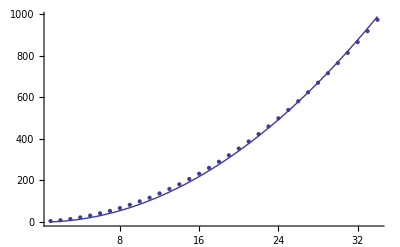

```mathematica
Show[ListPlot[rough],Plot[a*x^2/.fit,{x,1,Length[rough]}]]
```

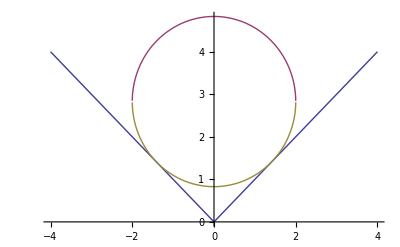

```mathematica
Plot[{Abs[x],Sqrt[4-x^2]+2 Sqrt[2],-Sqrt[4-x^2]+2 Sqrt[2]},{x,-4,4}]
```

(^ me being triumphant)